Here is the data set.

```mathematica
data={{0.00632,18,2.31,0,0.538,6.575,65.2,4.09,1,296,15.3,396.9,4.98,24},{0.02731,0,7.07,0,0.469,6.421,78.9,4.9671,2,242,17.8,396.9,9.14,21.6},{0.02729,0,7.07,0,0.469,7.185,61.1,4.9671,2,242,17.8,392.83,4.03,34.7},{0.03237,0,2.18,0,0.458,6.998,45.8,6.0622,3,222,18.7,394.63,2.94,33.4},{0.06905,0,2.18,0,0.458,7.147,54.2,6.0622,3,222,18.7,396.9,5.33,36.2},{0.02985,0,2.18,0,0.458,6.43,58.7,6.0622,3,222,18.7,394.12,5.21,28.7},{0.08829,12.5,7.87,0,0.524,6.012,66.6,5.5605,5,311,15.2,395.6,12.43,22.9},{0.14455,12.5,7.87,0,0.524,6.172,96.1,5.9505,5,311,15.2,396.9,19.15,27.1},{0.21124,12.5,7.87,0,0.524,5.631,100,6.0821,5,311,15.2,386.63,29.93,16.5},{0.17004,12.5,7.87,0,0.524,6.004,85.9,6.5921,5,311,15.2,386.71,17.1,18.9},{0.22489,12.5,7.87,0,0.524,6.377,94.3,6.3467,5,311,15.2,392.52,20.45,15},{0.11747,12.5,7.87,0,0.524,6.009,82.9,6.2267,5,311,15.2,396.9,13.27,18.9},{0.09378,12.5,7.87,0,0.524,5.889,39,5.4509,5,311,15.2,390.5,15.71,21.7},{0.62976,0,8.14,0,0.538,5.949,61.8,4.7075,4,307,21,396.9,8.26,20.4},{0.63796,0,8.14,0,0.538,6.096,84.5,4.4619,4,307,21,380.02,10.26,18.2},{0.62739,0,8.14,0,0.538,5.834,56.5,4.4986,4,307,21,395.62,8.47,19.9},{1.05393,0,8.14,0,0.538,5.935,29.3,4.4986,4,307,21,386.85,6.58,23.1},{0.7842,0,8.14,0,0.538,5.99,81.7,4.2579,4,307,21,386.75,14.67,17.5},{0.80271,0,8.14,0,0.538,5.456,36.6,3.7965,4,307,21,288.99,11.69,20.2},{0.7258,0,8.14,0,0.538,5.727,69.5,3.7965,4,307,21,390.95,11.28,18.2},{1.25179,0,8.14,0,0.538,5.57,98.1,3.7979,4,307,21,376.57,21.02,13.6},{0.85204,0,8.14,0,0.538,5.965,89.2,4.0123,4,307,21,392.53,13.83,19.6},{1.23247,0,8.14,0,0.538,6.142,91.7,3.9769,4,307,21,396.9,18.72,15.2},{0.98843,0,8.14,0,0.538,5.813,100,4.0952,4,307,21,394.54,19.88,14.5},{0.75026,0,8.14,0,0.538,5.924,94.1,4.3996,4,307,21,394.33,16.3,15.6},{0.84054,0,8.14,0,0.538,5.599,85.7,4.4546,4,307,21,303.42,16.51,13.9},{0.67191,0,8.14,0,0.538,5.813,90.3,4.682,4,307,21,376.88,14.81,16.6},{0.95577,0,8.14,0,0.538,6.047,88.8,4.4534,4,307,21,306.38,17.28,14.8},{0.77299,0,8.14,0,0.538,6.495,94.4,4.4547,4,307,21,387.94,12.8,18.4},{1.00245,0,8.14,0,0.538,6.674,87.3,4.239,4,307,21,380.23,11.98,21},{1.13081,0,8.14,0,0.538,5.713,94.1,4.233,4,307,21,360.17,22.6,12.7},{1.35472,0,8.14,0,0.538,6.072,100,4.175,4,307,21,376.73,13.04,14.5},{1.38799,0,8.14,0,0.538,5.95,82,3.99,4,307,21,232.6,27.71,13.2},{1.15172,0,8.14,0,0.538,5.701,95,3.7872,4,307,21,358.77,18.35,13.1},{1.61282,0,8.14,0,0.538,6.096,96.9,3.7598,4,307,21,248.31,20.34,13.5},{0.06417,0,5.96,0,0.499,5.933,68.2,3.3603,5,279,19.2,396.9,9.68,18.9},{0.09744,0,5.96,0,0.499,5.841,61.4,3.3779,5,279,19.2,377.56,11.41,20},{0.08014,0,5.96,0,0.499,5.85,41.5,3.9342,5,279,19.2,396.9,8.77,21},{0.17505,0,5.96,0,0.499,5.966,30.2,3.8473,5,279,19.2,393.43,10.13,24.7},{0.02763,75,2.95,0,0.428,6.595,21.8,5.4011,3,252,18.3,395.63,4.32,30.8},{0.03359,75,2.95,0,0.428,7.024,15.8,5.4011,3,252,18.3,395.62,1.98,34.9},{0.12744,0,6.91,0,0.448,6.77,2.9,5.7209,3,233,17.9,385.41,4.84,26.6},{0.1415,0,6.91,0,0.448,6.169,6.6,5.7209,3,233,17.9,383.37,5.81,25.3},{0.15936,0,6.91,0,0.448,6.211,6.5,5.7209,3,233,17.9,394.46,7.44,24.7},{0.12269,0,6.91,0,0.448,6.069,40,5.7209,3,233,17.9,389.39,9.55,21.2},{0.17142,0,6.91,0,0.448,5.682,33.8,5.1004,3,233,17.9,396.9,10.21,19.3},{0.18836,0,6.91,0,0.448,5.786,33.3,5.1004,3,233,17.9,396.9,14.15,20},{0.22927,0,6.91,0,0.448,6.03,85.5,5.6894,3,233,17.9,392.74,18.8,16.6},{0.25387,0,6.91,0,0.448,5.399,95.3,5.87,3,233,17.9,396.9,30.81,14.4},{0.21977,0,6.91,0,0.448,5.602,62,6.0877,3,233,17.9,396.9,16.2,19.4},{0.08873,21,5.64,0,0.439,5.963,45.7,6.8147,4,243,16.8,395.56,13.45,19.7},{0.04337,21,5.64,0,0.439,6.115,63,6.8147,4,243,16.8,393.97,9.43,20.5},{0.0536,21,5.64,0,0.439,6.511,21.1,6.8147,4,243,16.8,396.9,5.28,25},{0.04981,21,5.64,0,0.439,5.998,21.4,6.8147,4,243,16.8,396.9,8.43,23.4},{0.0136,75,4,0,0.41,5.888,47.6,7.3197,3,469,21.1,396.9,14.8,18.9},{0.01311,90,1.22,0,0.403,7.249,21.9,8.6966,5,226,17.9,395.93,4.81,35.4},{0.02055,85,0.74,0,0.41,6.383,35.7,9.1876,2,313,17.3,396.9,5.77,24.7},{0.01432,100,1.32,0,0.411,6.816,40.5,8.3248,5,256,15.1,392.9,3.95,31.6},{0.15445,25,5.13,0,0.453,6.145,29.2,7.8148,8,284,19.7,390.68,6.86,23.3},{0.10328,25,5.13,0,0.453,5.927,47.2,6.932,8,284,19.7,396.9,9.22,19.6},{0.14932,25,5.13,0,0.453,5.741,66.2,7.2254,8,284,19.7,395.11,13.15,18.7},{0.17171,25,5.13,0,0.453,5.966,93.4,6.8185,8,284,19.7,378.08,14.44,16},{0.11027,25,5.13,0,0.453,6.456,67.8,7.2255,8,284,19.7,396.9,6.73,22.2},{0.1265,25,5.13,0,0.453,6.762,43.4,7.9809,8,284,19.7,395.58,9.5,25},{0.01951,17.5,1.38,0,0.4161,7.104,59.5,9.2229,3,216,18.6,393.24,8.05,33},{0.03584,80,3.37,0,0.398,6.29,17.8,6.6115,4,337,16.1,396.9,4.67,23.5},{0.04379,80,3.37,0,0.398,5.787,31.1,6.6115,4,337,16.1,396.9,10.24,19.4},{0.05789,12.5,6.07,0,0.409,5.878,21.4,6.498,4,345,18.9,396.21,8.1,22},{0.13554,12.5,6.07,0,0.409,5.594,36.8,6.498,4,345,18.9,396.9,13.09,17.4},{0.12816,12.5,6.07,0,0.409,5.885,33,6.498,4,345,18.9,396.9,8.79,20.9},{0.08826,0,10.81,0,0.413,6.417,6.6,5.2873,4,305,19.2,383.73,6.72,24.2},{0.15876,0,10.81,0,0.413,5.961,17.5,5.2873,4,305,19.2,376.94,9.88,21.7},{0.09164,0,10.81,0,0.413,6.065,7.8,5.2873,4,305,19.2,390.91,5.52,22.8},{0.19539,0,10.81,0,0.413,6.245,6.2,5.2873,4,305,19.2,377.17,7.54,23.4},{0.07896,0,12.83,0,0.437,6.273,6,4.2515,5,398,18.7,394.92,6.78,24.1},{0.09512,0,12.83,0,0.437,6.286,45,4.5026,5,398,18.7,383.23,8.94,21.4},{0.10153,0,12.83,0,0.437,6.279,74.5,4.0522,5,398,18.7,373.66,11.97,20},{0.08707,0,12.83,0,0.437,6.14,45.8,4.0905,5,398,18.7,386.96,10.27,20.8},{0.05646,0,12.83,0,0.437,6.232,53.7,5.0141,5,398,18.7,386.4,12.34,21.2},{0.08387,0,12.83,0,0.437,5.874,36.6,4.5026,5,398,18.7,396.06,9.1,20.3},{0.04113,25,4.86,0,0.426,6.727,33.5,5.4007,4,281,19,396.9,5.29,28},{0.04462,25,4.86,0,0.426,6.619,70.4,5.4007,4,281,19,395.63,7.22,23.9},{0.03659,25,4.86,0,0.426,6.302,32.2,5.4007,4,281,19,396.9,6.72,24.8},{0.03551,25,4.86,0,0.426,6.167,46.7,5.4007,4,281,19,390.64,7.51,22.9},{0.05059,0,4.49,0,0.449,6.389,48,4.7794,3,247,18.5,396.9,9.62,23.9},{0.05735,0,4.49,0,0.449,6.63,56.1,4.4377,3,247,18.5,392.3,6.53,26.6},{0.05188,0,4.49,0,0.449,6.015,45.1,4.4272,3,247,18.5,395.99,12.86,22.5},{0.07151,0,4.49,0,0.449,6.121,56.8,3.7476,3,247,18.5,395.15,8.44,22.2},{0.0566,0,3.41,0,0.489,7.007,86.3,3.4217,2,270,17.8,396.9,5.5,23.6},{0.05302,0,3.41,0,0.489,7.079,63.1,3.4145,2,270,17.8,396.06,5.7,28.7},{0.04684,0,3.41,0,0.489,6.417,66.1,3.0923,2,270,17.8,392.18,8.81,22.6},{0.03932,0,3.41,0,0.489,6.405,73.9,3.0921,2,270,17.8,393.55,8.2,22},{0.04203,28,15.04,0,0.464,6.442,53.6,3.6659,4,270,18.2,395.01,8.16,22.9},{0.02875,28,15.04,0,0.464,6.211,28.9,3.6659,4,270,18.2,396.33,6.21,25},{0.04294,28,15.04,0,0.464,6.249,77.3,3.615,4,270,18.2,396.9,10.59,20.6},{0.12204,0,2.89,0,0.445,6.625,57.8,3.4952,2,276,18,357.98,6.65,28.4},{0.11504,0,2.89,0,0.445,6.163,69.6,3.4952,2,276,18,391.83,11.34,21.4},{0.12083,0,2.89,0,0.445,8.069,76,3.4952,2,276,18,396.9,4.21,38.7},{0.08187,0,2.89,0,0.445,7.82,36.9,3.4952,2,276,18,393.53,3.57,43.8},{0.0686,0,2.89,0,0.445,7.416,62.5,3.4952,2,276,18,396.9,6.19,33.2},{0.14866,0,8.56,0,0.52,6.727,79.9,2.7778,5,384,20.9,394.76,9.42,27.5},{0.11432,0,8.56,0,0.52,6.781,71.3,2.8561,5,384,20.9,395.58,7.67,26.5},{0.22876,0,8.56,0,0.52,6.405,85.4,2.7147,5,384,20.9,70.8,10.63,18.6},{0.21161,0,8.56,0,0.52,6.137,87.4,2.7147,5,384,20.9,394.47,13.44,19.3},{0.1396,0,8.56,0,0.52,6.167,90,2.421,5,384,20.9,392.69,12.33,20.1},{0.13262,0,8.56,0,0.52,5.851,96.7,2.1069,5,384,20.9,394.05,16.47,19.5},{0.1712,0,8.56,0,0.52,5.836,91.9,2.211,5,384,20.9,395.67,18.66,19.5},{0.13117,0,8.56,0,0.52,6.127,85.2,2.1224,5,384,20.9,387.69,14.09,20.4},{0.12802,0,8.56,0,0.52,6.474,97.1,2.4329,5,384,20.9,395.24,12.27,19.8},{0.26363,0,8.56,0,0.52,6.229,91.2,2.5451,5,384,20.9,391.23,15.55,19.4},{0.10793,0,8.56,0,0.52,6.195,54.4,2.7778,5,384,20.9,393.49,13,21.7},{0.10084,0,10.01,0,0.547,6.715,81.6,2.6775,6,432,17.8,395.59,10.16,22.8},{0.12329,0,10.01,0,0.547,5.913,92.9,2.3534,6,432,17.8,394.95,16.21,18.8},{0.22212,0,10.01,0,0.547,6.092,95.4,2.548,6,432,17.8,396.9,17.09,18.7},{0.14231,0,10.01,0,0.547,6.254,84.2,2.2565,6,432,17.8,388.74,10.45,18.5},{0.17134,0,10.01,0,0.547,5.928,88.2,2.4631,6,432,17.8,344.91,15.76,18.3},{0.13158,0,10.01,0,0.547,6.176,72.5,2.7301,6,432,17.8,393.3,12.04,21.2},{0.15098,0,10.01,0,0.547,6.021,82.6,2.7474,6,432,17.8,394.51,10.3,19.2},{0.13058,0,10.01,0,0.547,5.872,73.1,2.4775,6,432,17.8,338.63,15.37,20.4},{0.14476,0,10.01,0,0.547,5.731,65.2,2.7592,6,432,17.8,391.5,13.61,19.3},{0.06899,0,25.65,0,0.581,5.87,69.7,2.2577,2,188,19.1,389.15,14.37,22},{0.07165,0,25.65,0,0.581,6.004,84.1,2.1974,2,188,19.1,377.67,14.27,20.3},{0.09299,0,25.65,0,0.581,5.961,92.9,2.0869,2,188,19.1,378.09,17.93,20.5},{0.15038,0,25.65,0,0.581,5.856,97,1.9444,2,188,19.1,370.31,25.41,17.3},{0.09849,0,25.65,0,0.581,5.879,95.8,2.0063,2,188,19.1,379.38,17.58,18.8},{0.16902,0,25.65,0,0.581,5.986,88.4,1.9929,2,188,19.1,385.02,14.81,21.4},{0.38735,0,25.65,0,0.581,5.613,95.6,1.7572,2,188,19.1,359.29,27.26,15.7},{0.25915,0,21.89,0,0.624,5.693,96,1.7883,4,437,21.2,392.11,17.19,16.2},{0.32543,0,21.89,0,0.624,6.431,98.8,1.8125,4,437,21.2,396.9,15.39,18},{0.88125,0,21.89,0,0.624,5.637,94.7,1.9799,4,437,21.2,396.9,18.34,14.3},{0.34006,0,21.89,0,0.624,6.458,98.9,2.1185,4,437,21.2,395.04,12.6,19.2},{1.19294,0,21.89,0,0.624,6.326,97.7,2.271,4,437,21.2,396.9,12.26,19.6},{0.59005,0,21.89,0,0.624,6.372,97.9,2.3274,4,437,21.2,385.76,11.12,23},{0.32982,0,21.89,0,0.624,5.822,95.4,2.4699,4,437,21.2,388.69,15.03,18.4},{0.97617,0,21.89,0,0.624,5.757,98.4,2.346,4,437,21.2,262.76,17.31,15.6},{0.55778,0,21.89,0,0.624,6.335,98.2,2.1107,4,437,21.2,394.67,16.96,18.1},{0.32264,0,21.89,0,0.624,5.942,93.5,1.9669,4,437,21.2,378.25,16.9,17.4},{0.35233,0,21.89,0,0.624,6.454,98.4,1.8498,4,437,21.2,394.08,14.59,17.1},{0.2498,0,21.89,0,0.624,5.857,98.2,1.6686,4,437,21.2,392.04,21.32,13.3},{0.54452,0,21.89,0,0.624,6.151,97.9,1.6687,4,437,21.2,396.9,18.46,17.8},{0.2909,0,21.89,0,0.624,6.174,93.6,1.6119,4,437,21.2,388.08,24.16,14},{1.62864,0,21.89,0,0.624,5.019,100,1.4394,4,437,21.2,396.9,34.41,14.4},{3.32105,0,19.58,1,0.871,5.403,100,1.3216,5,403,14.7,396.9,26.82,13.4},{4.0974,0,19.58,0,0.871,5.468,100,1.4118,5,403,14.7,396.9,26.42,15.6},{2.77974,0,19.58,0,0.871,4.903,97.8,1.3459,5,403,14.7,396.9,29.29,11.8},{2.37934,0,19.58,0,0.871,6.13,100,1.4191,5,403,14.7,172.91,27.8,13.8},{2.15505,0,19.58,0,0.871,5.628,100,1.5166,5,403,14.7,169.27,16.65,15.6},{2.36862,0,19.58,0,0.871,4.926,95.7,1.4608,5,403,14.7,391.71,29.53,14.6},{2.33099,0,19.58,0,0.871,5.186,93.8,1.5296,5,403,14.7,356.99,28.32,17.8},{2.73397,0,19.58,0,0.871,5.597,94.9,1.5257,5,403,14.7,351.85,21.45,15.4},{1.6566,0,19.58,0,0.871,6.122,97.3,1.618,5,403,14.7,372.8,14.1,21.5},{1.49632,0,19.58,0,0.871,5.404,100,1.5916,5,403,14.7,341.6,13.28,19.6},{1.12658,0,19.58,1,0.871,5.012,88,1.6102,5,403,14.7,343.28,12.12,15.3},{2.14918,0,19.58,0,0.871,5.709,98.5,1.6232,5,403,14.7,261.95,15.79,19.4},{1.41385,0,19.58,1,0.871,6.129,96,1.7494,5,403,14.7,321.02,15.12,17},{3.53501,0,19.58,1,0.871,6.152,82.6,1.7455,5,403,14.7,88.01,15.02,15.6},{2.44668,0,19.58,0,0.871,5.272,94,1.7364,5,403,14.7,88.63,16.14,13.1},{1.22358,0,19.58,0,0.605,6.943,97.4,1.8773,5,403,14.7,363.43,4.59,41.3},{1.34284,0,19.58,0,0.605,6.066,100,1.7573,5,403,14.7,353.89,6.43,24.3},{1.42502,0,19.58,0,0.871,6.51,100,1.7659,5,403,14.7,364.31,7.39,23.3},{1.27346,0,19.58,1,0.605,6.25,92.6,1.7984,5,403,14.7,338.92,5.5,27},{1.46336,0,19.58,0,0.605,7.489,90.8,1.9709,5,403,14.7,374.43,1.73,50},{1.83377,0,19.58,1,0.605,7.802,98.2,2.0407,5,403,14.7,389.61,1.92,50},{1.51902,0,19.58,1,0.605,8.375,93.9,2.162,5,403,14.7,388.45,3.32,50},{2.24236,0,19.58,0,0.605,5.854,91.8,2.422,5,403,14.7,395.11,11.64,22.7},{2.924,0,19.58,0,0.605,6.101,93,2.2834,5,403,14.7,240.16,9.81,25},{2.01019,0,19.58,0,0.605,7.929,96.2,2.0459,5,403,14.7,369.3,3.7,50},{1.80028,0,19.58,0,0.605,5.877,79.2,2.4259,5,403,14.7,227.61,12.14,23.8},{2.3004,0,19.58,0,0.605,6.319,96.1,2.1,5,403,14.7,297.09,11.1,23.8},{2.44953,0,19.58,0,0.605,6.402,95.2,2.2625,5,403,14.7,330.04,11.32,22.3},{1.20742,0,19.58,0,0.605,5.875,94.6,2.4259,5,403,14.7,292.29,14.43,17.4},{2.3139,0,19.58,0,0.605,5.88,97.3,2.3887,5,403,14.7,348.13,12.03,19.1},{0.13914,0,4.05,0,0.51,5.572,88.5,2.5961,5,296,16.6,396.9,14.69,23.1},{0.09178,0,4.05,0,0.51,6.416,84.1,2.6463,5,296,16.6,395.5,9.04,23.6},{0.08447,0,4.05,0,0.51,5.859,68.7,2.7019,5,296,16.6,393.23,9.64,22.6},{0.06664,0,4.05,0,0.51,6.546,33.1,3.1323,5,296,16.6,390.96,5.33,29.4},{0.07022,0,4.05,0,0.51,6.02,47.2,3.5549,5,296,16.6,393.23,10.11,23.2},{0.05425,0,4.05,0,0.51,6.315,73.4,3.3175,5,296,16.6,395.6,6.29,24.6},{0.06642,0,4.05,0,0.51,6.86,74.4,2.9153,5,296,16.6,391.27,6.92,29.9},{0.0578,0,2.46,0,0.488,6.98,58.4,2.829,3,193,17.8,396.9,5.04,37.2},{0.06588,0,2.46,0,0.488,7.765,83.3,2.741,3,193,17.8,395.56,7.56,39.8},{0.06888,0,2.46,0,0.488,6.144,62.2,2.5979,3,193,17.8,396.9,9.45,36.2},{0.09103,0,2.46,0,0.488,7.155,92.2,2.7006,3,193,17.8,394.12,4.82,37.9},{0.10008,0,2.46,0,0.488,6.563,95.6,2.847,3,193,17.8,396.9,5.68,32.5},{0.08308,0,2.46,0,0.488,5.604,89.8,2.9879,3,193,17.8,391,13.98,26.4},{0.06047,0,2.46,0,0.488,6.153,68.8,3.2797,3,193,17.8,387.11,13.15,29.6},{0.05602,0,2.46,0,0.488,7.831,53.6,3.1992,3,193,17.8,392.63,4.45,50},{0.07875,45,3.44,0,0.437,6.782,41.1,3.7886,5,398,15.2,393.87,6.68,32},{0.12579,45,3.44,0,0.437,6.556,29.1,4.5667,5,398,15.2,382.84,4.56,29.8},{0.0837,45,3.44,0,0.437,7.185,38.9,4.5667,5,398,15.2,396.9,5.39,34.9},{0.09068,45,3.44,0,0.437,6.951,21.5,6.4798,5,398,15.2,377.68,5.1,37},{0.06911,45,3.44,0,0.437,6.739,30.8,6.4798,5,398,15.2,389.71,4.69,30.5},{0.08664,45,3.44,0,0.437,7.178,26.3,6.4798,5,398,15.2,390.49,2.87,36.4},{0.02187,60,2.93,0,0.401,6.8,9.9,6.2196,1,265,15.6,393.37,5.03,31.1},{0.01439,60,2.93,0,0.401,6.604,18.8,6.2196,1,265,15.6,376.7,4.38,29.1},{0.01381,80,0.46,0,0.422,7.875,32,5.6484,4,255,14.4,394.23,2.97,50},{0.04011,80,1.52,0,0.404,7.287,34.1,7.309,2,329,12.6,396.9,4.08,33.3},{0.04666,80,1.52,0,0.404,7.107,36.6,7.309,2,329,12.6,354.31,8.61,30.3},{0.03768,80,1.52,0,0.404,7.274,38.3,7.309,2,329,12.6,392.2,6.62,34.6},{0.0315,95,1.47,0,0.403,6.975,15.3,7.6534,3,402,17,396.9,4.56,34.9},{0.01778,95,1.47,0,0.403,7.135,13.9,7.6534,3,402,17,384.3,4.45,32.9},{0.03445,82.5,2.03,0,0.415,6.162,38.4,6.27,2,348,14.7,393.77,7.43,24.1},{0.02177,82.5,2.03,0,0.415,7.61,15.7,6.27,2,348,14.7,395.38,3.11,42.3},{0.0351,95,2.68,0,0.4161,7.853,33.2,5.118,4,224,14.7,392.78,3.81,48.5},{0.02009,95,2.68,0,0.4161,8.034,31.9,5.118,4,224,14.7,390.55,2.88,50},{0.13642,0,10.59,0,0.489,5.891,22.3,3.9454,4,277,18.6,396.9,10.87,22.6},{0.22969,0,10.59,0,0.489,6.326,52.5,4.3549,4,277,18.6,394.87,10.97,24.4},{0.25199,0,10.59,0,0.489,5.783,72.7,4.3549,4,277,18.6,389.43,18.06,22.5},{0.13587,0,10.59,1,0.489,6.064,59.1,4.2392,4,277,18.6,381.32,14.66,24.4},{0.43571,0,10.59,1,0.489,5.344,100,3.875,4,277,18.6,396.9,23.09,20},{0.17446,0,10.59,1,0.489,5.96,92.1,3.8771,4,277,18.6,393.25,17.27,21.7},{0.37578,0,10.59,1,0.489,5.404,88.6,3.665,4,277,18.6,395.24,23.98,19.3},{0.21719,0,10.59,1,0.489,5.807,53.8,3.6526,4,277,18.6,390.94,16.03,22.4},{0.14052,0,10.59,0,0.489,6.375,32.3,3.9454,4,277,18.6,385.81,9.38,28.1},{0.28955,0,10.59,0,0.489,5.412,9.8,3.5875,4,277,18.6,348.93,29.55,23.7},{0.19802,0,10.59,0,0.489,6.182,42.4,3.9454,4,277,18.6,393.63,9.47,25},{0.0456,0,13.89,1,0.55,5.888,56,3.1121,5,276,16.4,392.8,13.51,23.3},{0.07013,0,13.89,0,0.55,6.642,85.1,3.4211,5,276,16.4,392.78,9.69,28.7},{0.11069,0,13.89,1,0.55,5.951,93.8,2.8893,5,276,16.4,396.9,17.92,21.5},{0.11425,0,13.89,1,0.55,6.373,92.4,3.3633,5,276,16.4,393.74,10.5,23},{0.35809,0,6.2,1,0.507,6.951,88.5,2.8617,8,307,17.4,391.7,9.71,26.7},{0.40771,0,6.2,1,0.507,6.164,91.3,3.048,8,307,17.4,395.24,21.46,21.7},{0.62356,0,6.2,1,0.507,6.879,77.7,3.2721,8,307,17.4,390.39,9.93,27.5},{0.6147,0,6.2,0,0.507,6.618,80.8,3.2721,8,307,17.4,396.9,7.6,30.1},{0.31533,0,6.2,0,0.504,8.266,78.3,2.8944,8,307,17.4,385.05,4.14,44.8},{0.52693,0,6.2,0,0.504,8.725,83,2.8944,8,307,17.4,382,4.63,50},{0.38214,0,6.2,0,0.504,8.04,86.5,3.2157,8,307,17.4,387.38,3.13,37.6},{0.41238,0,6.2,0,0.504,7.163,79.9,3.2157,8,307,17.4,372.08,6.36,31.6},{0.29819,0,6.2,0,0.504,7.686,17,3.3751,8,307,17.4,377.51,3.92,46.7},{0.44178,0,6.2,0,0.504,6.552,21.4,3.3751,8,307,17.4,380.34,3.76,31.5},{0.537,0,6.2,0,0.504,5.981,68.1,3.6715,8,307,17.4,378.35,11.65,24.3},{0.46296,0,6.2,0,0.504,7.412,76.9,3.6715,8,307,17.4,376.14,5.25,31.7},{0.57529,0,6.2,0,0.507,8.337,73.3,3.8384,8,307,17.4,385.91,2.47,41.7},{0.33147,0,6.2,0,0.507,8.247,70.4,3.6519,8,307,17.4,378.95,3.95,48.3},{0.44791,0,6.2,1,0.507,6.726,66.5,3.6519,8,307,17.4,360.2,8.05,29},{0.33045,0,6.2,0,0.507,6.086,61.5,3.6519,8,307,17.4,376.75,10.88,24},{0.52058,0,6.2,1,0.507,6.631,76.5,4.148,8,307,17.4,388.45,9.54,25.1},{0.51183,0,6.2,0,0.507,7.358,71.6,4.148,8,307,17.4,390.07,4.73,31.5},{0.08244,30,4.93,0,0.428,6.481,18.5,6.1899,6,300,16.6,379.41,6.36,23.7},{0.09252,30,4.93,0,0.428,6.606,42.2,6.1899,6,300,16.6,383.78,7.37,23.3},{0.11329,30,4.93,0,0.428,6.897,54.3,6.3361,6,300,16.6,391.25,11.38,22},{0.10612,30,4.93,0,0.428,6.095,65.1,6.3361,6,300,16.6,394.62,12.4,20.1},{0.1029,30,4.93,0,0.428,6.358,52.9,7.0355,6,300,16.6,372.75,11.22,22.2},{0.12757,30,4.93,0,0.428,6.393,7.8,7.0355,6,300,16.6,374.71,5.19,23.7},{0.20608,22,5.86,0,0.431,5.593,76.5,7.9549,7,330,19.1,372.49,12.5,17.6},{0.19133,22,5.86,0,0.431,5.605,70.2,7.9549,7,330,19.1,389.13,18.46,18.5},{0.33983,22,5.86,0,0.431,6.108,34.9,8.0555,7,330,19.1,390.18,9.16,24.3},{0.19657,22,5.86,0,0.431,6.226,79.2,8.0555,7,330,19.1,376.14,10.15,20.5},{0.16439,22,5.86,0,0.431,6.433,49.1,7.8265,7,330,19.1,374.71,9.52,24.5},{0.19073,22,5.86,0,0.431,6.718,17.5,7.8265,7,330,19.1,393.74,6.56,26.2},{0.1403,22,5.86,0,0.431,6.487,13,7.3967,7,330,19.1,396.28,5.9,24.4},{0.21409,22,5.86,0,0.431,6.438,8.9,7.3967,7,330,19.1,377.07,3.59,24.8},{0.08221,22,5.86,0,0.431,6.957,6.8,8.9067,7,330,19.1,386.09,3.53,29.6},{0.36894,22,5.86,0,0.431,8.259,8.4,8.9067,7,330,19.1,396.9,3.54,42.8},{0.04819,80,3.64,0,0.392,6.108,32,9.2203,1,315,16.4,392.89,6.57,21.9},{0.03548,80,3.64,0,0.392,5.876,19.1,9.2203,1,315,16.4,395.18,9.25,20.9},{0.01538,90,3.75,0,0.394,7.454,34.2,6.3361,3,244,15.9,386.34,3.11,44},{0.61154,20,3.97,0,0.647,8.704,86.9,1.801,5,264,13,389.7,5.12,50},{0.66351,20,3.97,0,0.647,7.333,100,1.8946,5,264,13,383.29,7.79,36},{0.65665,20,3.97,0,0.647,6.842,100,2.0107,5,264,13,391.93,6.9,30.1},{0.54011,20,3.97,0,0.647,7.203,81.8,2.1121,5,264,13,392.8,9.59,33.8},{0.53412,20,3.97,0,0.647,7.52,89.4,2.1398,5,264,13,388.37,7.26,43.1},{0.52014,20,3.97,0,0.647,8.398,91.5,2.2885,5,264,13,386.86,5.91,48.8},{0.82526,20,3.97,0,0.647,7.327,94.5,2.0788,5,264,13,393.42,11.25,31},{0.55007,20,3.97,0,0.647,7.206,91.6,1.9301,5,264,13,387.89,8.1,36.5},{0.76162,20,3.97,0,0.647,5.56,62.8,1.9865,5,264,13,392.4,10.45,22.8},{0.7857,20,3.97,0,0.647,7.014,84.6,2.1329,5,264,13,384.07,14.79,30.7},{0.57834,20,3.97,0,0.575,8.297,67,2.4216,5,264,13,384.54,7.44,50},{0.5405,20,3.97,0,0.575,7.47,52.6,2.872,5,264,13,390.3,3.16,43.5},{0.09065,20,6.96,1,0.464,5.92,61.5,3.9175,3,223,18.6,391.34,13.65,20.7},{0.29916,20,6.96,0,0.464,5.856,42.1,4.429,3,223,18.6,388.65,13,21.1},{0.16211,20,6.96,0,0.464,6.24,16.3,4.429,3,223,18.6,396.9,6.59,25.2},{0.1146,20,6.96,0,0.464,6.538,58.7,3.9175,3,223,18.6,394.96,7.73,24.4},{0.22188,20,6.96,1,0.464,7.691,51.8,4.3665,3,223,18.6,390.77,6.58,35.2},{0.05644,40,6.41,1,0.447,6.758,32.9,4.0776,4,254,17.6,396.9,3.53,32.4},{0.09604,40,6.41,0,0.447,6.854,42.8,4.2673,4,254,17.6,396.9,2.98,32},{0.10469,40,6.41,1,0.447,7.267,49,4.7872,4,254,17.6,389.25,6.05,33.2},{0.06127,40,6.41,1,0.447,6.826,27.6,4.8628,4,254,17.6,393.45,4.16,33.1},{0.07978,40,6.41,0,0.447,6.482,32.1,4.1403,4,254,17.6,396.9,7.19,29.1},{0.21038,20,3.33,0,0.4429,6.812,32.2,4.1007,5,216,14.9,396.9,4.85,35.1},{0.03578,20,3.33,0,0.4429,7.82,64.5,4.6947,5,216,14.9,387.31,3.76,45.4},{0.03705,20,3.33,0,0.4429,6.968,37.2,5.2447,5,216,14.9,392.23,4.59,35.4},{0.06129,20,3.33,1,0.4429,7.645,49.7,5.2119,5,216,14.9,377.07,3.01,46},{0.01501,90,1.21,1,0.401,7.923,24.8,5.885,1,198,13.6,395.52,3.16,50},{0.00906,90,2.97,0,0.4,7.088,20.8,7.3073,1,285,15.3,394.72,7.85,32.2},{0.01096,55,2.25,0,0.389,6.453,31.9,7.3073,1,300,15.3,394.72,8.23,22},{0.01965,80,1.76,0,0.385,6.23,31.5,9.0892,1,241,18.2,341.6,12.93,20.1},{0.03871,52.5,5.32,0,0.405,6.209,31.3,7.3172,6,293,16.6,396.9,7.14,23.2},{0.0459,52.5,5.32,0,0.405,6.315,45.6,7.3172,6,293,16.6,396.9,7.6,22.3},{0.04297,52.5,5.32,0,0.405,6.565,22.9,7.3172,6,293,16.6,371.72,9.51,24.8},{0.03502,80,4.95,0,0.411,6.861,27.9,5.1167,4,245,19.2,396.9,3.33,28.5},{0.07886,80,4.95,0,0.411,7.148,27.7,5.1167,4,245,19.2,396.9,3.56,37.3},{0.03615,80,4.95,0,0.411,6.63,23.4,5.1167,4,245,19.2,396.9,4.7,27.9},{0.08265,0,13.92,0,0.437,6.127,18.4,5.5027,4,289,16,396.9,8.58,23.9},{0.08199,0,13.92,0,0.437,6.009,42.3,5.5027,4,289,16,396.9,10.4,21.7},{0.12932,0,13.92,0,0.437,6.678,31.1,5.9604,4,289,16,396.9,6.27,28.6},{0.05372,0,13.92,0,0.437,6.549,51,5.9604,4,289,16,392.85,7.39,27.1},{0.14103,0,13.92,0,0.437,5.79,58,6.32,4,289,16,396.9,15.84,20.3},{0.06466,70,2.24,0,0.4,6.345,20.1,7.8278,5,358,14.8,368.24,4.97,22.5},{0.05561,70,2.24,0,0.4,7.041,10,7.8278,5,358,14.8,371.58,4.74,29},{0.04417,70,2.24,0,0.4,6.871,47.4,7.8278,5,358,14.8,390.86,6.07,24.8},{0.03537,34,6.09,0,0.433,6.59,40.4,5.4917,7,329,16.1,395.75,9.5,22},{0.09266,34,6.09,0,0.433,6.495,18.4,5.4917,7,329,16.1,383.61,8.67,26.4},{0.1,34,6.09,0,0.433,6.982,17.7,5.4917,7,329,16.1,390.43,4.86,33.1},{0.05515,33,2.18,0,0.472,7.236,41.1,4.022,7,222,18.4,393.68,6.93,36.1},{0.05479,33,2.18,0,0.472,6.616,58.1,3.37,7,222,18.4,393.36,8.93,28.4},{0.07503,33,2.18,0,0.472,7.42,71.9,3.0992,7,222,18.4,396.9,6.47,33.4},{0.04932,33,2.18,0,0.472,6.849,70.3,3.1827,7,222,18.4,396.9,7.53,28.2},{0.49298,0,9.9,0,0.544,6.635,82.5,3.3175,4,304,18.4,396.9,4.54,22.8},{0.3494,0,9.9,0,0.544,5.972,76.7,3.1025,4,304,18.4,396.24,9.97,20.3},{2.63548,0,9.9,0,0.544,4.973,37.8,2.5194,4,304,18.4,350.45,12.64,16.1},{0.79041,0,9.9,0,0.544,6.122,52.8,2.6403,4,304,18.4,396.9,5.98,22.1},{0.26169,0,9.9,0,0.544,6.023,90.4,2.834,4,304,18.4,396.3,11.72,19.4},{0.26938,0,9.9,0,0.544,6.266,82.8,3.2628,4,304,18.4,393.39,7.9,21.6},{0.3692,0,9.9,0,0.544,6.567,87.3,3.6023,4,304,18.4,395.69,9.28,23.8},{0.25356,0,9.9,0,0.544,5.705,77.7,3.945,4,304,18.4,396.42,11.5,16.2},{0.31827,0,9.9,0,0.544,5.914,83.2,3.9986,4,304,18.4,390.7,18.33,17.8},{0.24522,0,9.9,0,0.544,5.782,71.7,4.0317,4,304,18.4,396.9,15.94,19.8},{0.40202,0,9.9,0,0.544,6.382,67.2,3.5325,4,304,18.4,395.21,10.36,23.1},{0.47547,0,9.9,0,0.544,6.113,58.8,4.0019,4,304,18.4,396.23,12.73,21},{0.1676,0,7.38,0,0.493,6.426,52.3,4.5404,5,287,19.6,396.9,7.2,23.8},{0.18159,0,7.38,0,0.493,6.376,54.3,4.5404,5,287,19.6,396.9,6.87,23.1},{0.35114,0,7.38,0,0.493,6.041,49.9,4.7211,5,287,19.6,396.9,7.7,20.4},{0.28392,0,7.38,0,0.493,5.708,74.3,4.7211,5,287,19.6,391.13,11.74,18.5},{0.34109,0,7.38,0,0.493,6.415,40.1,4.7211,5,287,19.6,396.9,6.12,25},{0.19186,0,7.38,0,0.493,6.431,14.7,5.4159,5,287,19.6,393.68,5.08,24.6},{0.30347,0,7.38,0,0.493,6.312,28.9,5.4159,5,287,19.6,396.9,6.15,23},{0.24103,0,7.38,0,0.493,6.083,43.7,5.4159,5,287,19.6,396.9,12.79,22.2},{0.06617,0,3.24,0,0.46,5.868,25.8,5.2146,4,430,16.9,382.44,9.97,19.3},{0.06724,0,3.24,0,0.46,6.333,17.2,5.2146,4,430,16.9,375.21,7.34,22.6},{0.04544,0,3.24,0,0.46,6.144,32.2,5.8736,4,430,16.9,368.57,9.09,19.8},{0.05023,35,6.06,0,0.4379,5.706,28.4,6.6407,1,304,16.9,394.02,12.43,17.1},{0.03466,35,6.06,0,0.4379,6.031,23.3,6.6407,1,304,16.9,362.25,7.83,19.4},{0.05083,0,5.19,0,0.515,6.316,38.1,6.4584,5,224,20.2,389.71,5.68,22.2},{0.03738,0,5.19,0,0.515,6.31,38.5,6.4584,5,224,20.2,389.4,6.75,20.7},{0.03961,0,5.19,0,0.515,6.037,34.5,5.9853,5,224,20.2,396.9,8.01,21.1},{0.03427,0,5.19,0,0.515,5.869,46.3,5.2311,5,224,20.2,396.9,9.8,19.5},{0.03041,0,5.19,0,0.515,5.895,59.6,5.615,5,224,20.2,394.81,10.56,18.5},{0.03306,0,5.19,0,0.515,6.059,37.3,4.8122,5,224,20.2,396.14,8.51,20.6},{0.05497,0,5.19,0,0.515,5.985,45.4,4.8122,5,224,20.2,396.9,9.74,19},{0.06151,0,5.19,0,0.515,5.968,58.5,4.8122,5,224,20.2,396.9,9.29,18.7},{0.01301,35,1.52,0,0.442,7.241,49.3,7.0379,1,284,15.5,394.74,5.49,32.7},{0.02498,0,1.89,0,0.518,6.54,59.7,6.2669,1,422,15.9,389.96,8.65,16.5},{0.02543,55,3.78,0,0.484,6.696,56.4,5.7321,5,370,17.6,396.9,7.18,23.9},{0.03049,55,3.78,0,0.484,6.874,28.1,6.4654,5,370,17.6,387.97,4.61,31.2},{0.03113,0,4.39,0,0.442,6.014,48.5,8.0136,3,352,18.8,385.64,10.53,17.5},{0.06162,0,4.39,0,0.442,5.898,52.3,8.0136,3,352,18.8,364.61,12.67,17.2},{0.0187,85,4.15,0,0.429,6.516,27.7,8.5353,4,351,17.9,392.43,6.36,23.1},{0.01501,80,2.01,0,0.435,6.635,29.7,8.344,4,280,17,390.94,5.99,24.5},{0.02899,40,1.25,0,0.429,6.939,34.5,8.7921,1,335,19.7,389.85,5.89,26.6},{0.06211,40,1.25,0,0.429,6.49,44.4,8.7921,1,335,19.7,396.9,5.98,22.9},{0.0795,60,1.69,0,0.411,6.579,35.9,10.7103,4,411,18.3,370.78,5.49,24.1},{0.07244,60,1.69,0,0.411,5.884,18.5,10.7103,4,411,18.3,392.33,7.79,18.6},{0.01709,90,2.02,0,0.41,6.728,36.1,12.1265,5,187,17,384.46,4.5,30.1},{0.04301,80,1.91,0,0.413,5.663,21.9,10.5857,4,334,22,382.8,8.05,18.2},{0.10659,80,1.91,0,0.413,5.936,19.5,10.5857,4,334,22,376.04,5.57,20.6},{8.98296,0,18.1,1,0.77,6.212,97.4,2.1222,24,666,20.2,377.73,17.6,17.8},{3.8497,0,18.1,1,0.77,6.395,91,2.5052,24,666,20.2,391.34,13.27,21.7},{5.20177,0,18.1,1,0.77,6.127,83.4,2.7227,24,666,20.2,395.43,11.48,22.7},{4.26131,0,18.1,0,0.77,6.112,81.3,2.5091,24,666,20.2,390.74,12.67,22.6},{4.54192,0,18.1,0,0.77,6.398,88,2.5182,24,666,20.2,374.56,7.79,25},{3.83684,0,18.1,0,0.77,6.251,91.1,2.2955,24,666,20.2,350.65,14.19,19.9},{3.67822,0,18.1,0,0.77,5.362,96.2,2.1036,24,666,20.2,380.79,10.19,20.8},{4.22239,0,18.1,1,0.77,5.803,89,1.9047,24,666,20.2,353.04,14.64,16.8},{3.47428,0,18.1,1,0.718,8.78,82.9,1.9047,24,666,20.2,354.55,5.29,21.9},{4.55587,0,18.1,0,0.718,3.561,87.9,1.6132,24,666,20.2,354.7,7.12,27.5},{3.69695,0,18.1,0,0.718,4.963,91.4,1.7523,24,666,20.2,316.03,14,21.9}};
```

## Question 3-3(a)

We can take a few columns of the data by specifying their parts.  For example, if we want to plot the Per Capita crime rate (Column 1) versus the housing price (Column 14), we would do the following:

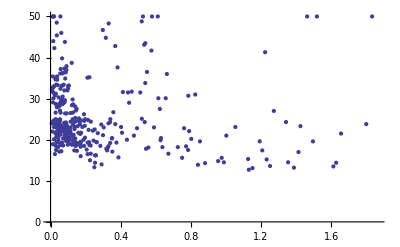

```mathematica
datapoints1=data[[All,{1,14}]];
ListPlot[datapoints1]
```